```mathematica
Exp[x/(365+x)*Log[(365+x)/x]+365/(365+x)*Log[(365+x)]]-365//FullSimplify
```

-365+(365+x)^(365/(365+x)) ((365+x)/x)^(x/(365+x))

```mathematica
Series[-365+(365+x)^(365/(365+x)) ((365+x)/x)^(x/(365+x)),{x,0,2}]
```

(1-Log[5]-Log[73]+Log[365/x]) x+1/730 (Log[5]^2+2 Log[5] Log[73]+Log[73]^2-2 Log[5] Log[365/x]-2 Log[73] Log[365/x]+Log[365/x]^2) x^2+O[x]^3

```mathematica
(1-Log[5]-Log[73]+Log[365/x])x//FullSimplify
```

x (1+Log[1/x])

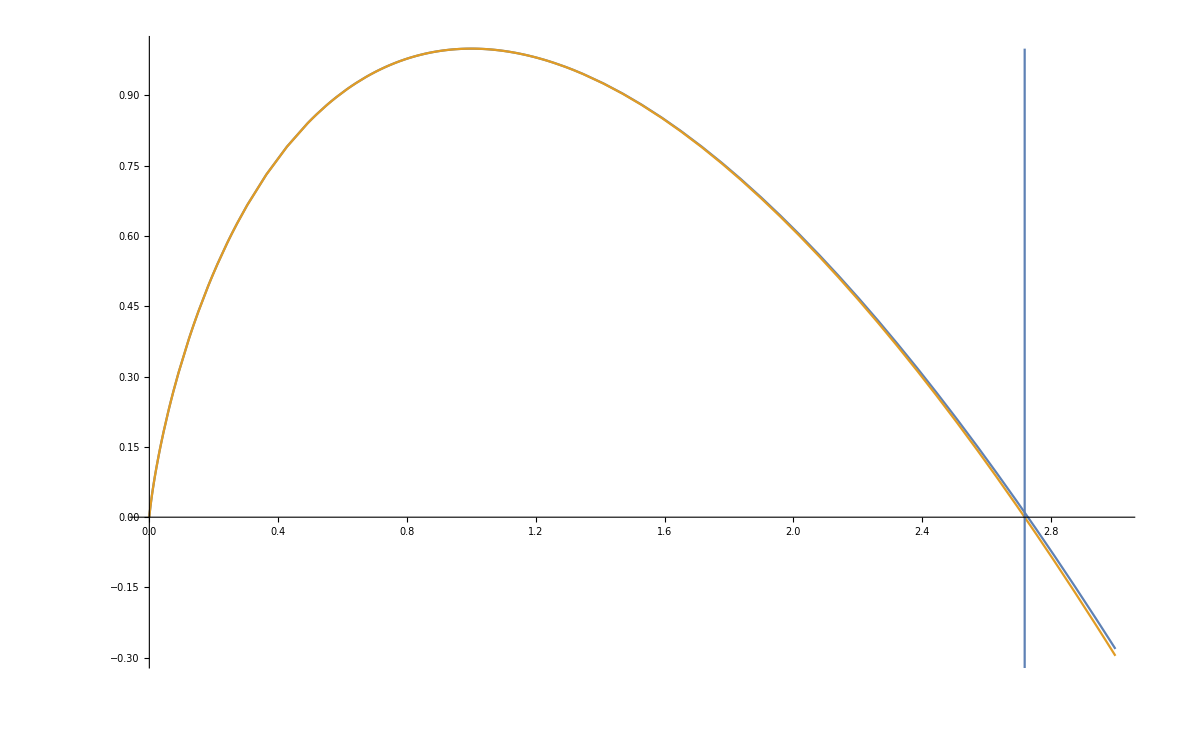

```mathematica
Show[Plot[{%295-365,x (1-Log[x])},{x,0,3}],ParametricPlot[{E,t},{t,-1,1}]]
```

```mathematica
Log2[365.]
Log2[27.]
%/%%
```

8.51175

4.75489

0.558626